## BFKL Plot

```mathematica
Y={(ⅇ^-τ ((-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2)))+ⅇ^((2 (σ+(𝕧+√(1+𝕧^2)) τ))/(√(1+𝕧^2)))+𝕧-√(1+𝕧^2)-ⅇ^(2 τ) (𝕧+√(1+𝕧^2))) Cosh[σ]-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) (-1+ⅇ^(2 τ)) √(1+𝕧^2) Sinh[σ]))/(2 (1+ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) 𝕧)),(ⅇ^-τ ((ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2)))+ⅇ^((2 (σ+(𝕧+√(1+𝕧^2)) τ))/(√(1+𝕧^2)))-𝕧+√(1+𝕧^2)-ⅇ^(2 τ) (𝕧+√(1+𝕧^2))) Cosh[σ]-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) (1+ⅇ^(2 τ)) √(1+𝕧^2) Sinh[σ]))/(2 (1+ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) 𝕧)),(ⅇ^-τ (-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) (-1+ⅇ^(2 τ)) √(1+𝕧^2) Cosh[σ]-(ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2)))-ⅇ^((2 (σ+(𝕧+√(1+𝕧^2)) τ))/(√(1+𝕧^2)))-𝕧+√(1+𝕧^2)+ⅇ^(2 τ) (𝕧+√(1+𝕧^2))) Sinh[σ]))/(2 (1+ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) 𝕧)),(ⅇ^-τ (-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) (1+ⅇ^(2 τ)) √(1+𝕧^2) Cosh[σ]-(-ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2)))-ⅇ^((2 (σ+(𝕧+√(1+𝕧^2)) τ))/(√(1+𝕧^2)))+𝕧-√(1+𝕧^2)+ⅇ^(2 τ) (𝕧+√(1+𝕧^2))) Sinh[σ]))/(2 (1+ⅇ^((2 (σ+𝕧 τ))/(√(1+𝕧^2))) 𝕧))};
```

```mathematica
𝓋=1/20;
```

```mathematica
fn[u_,v_]={r Cos[ϕ],r Sin[ϕ],Mod[t,-π,π/4]}/.{r->ArcTan[√(Y⟦2⟧^2+Y⟦3⟧^2)],Sin[ϕ]-> Y⟦3⟧/(√(Y⟦2⟧^2+Y⟦3⟧^2)),Cos[ϕ]->Y⟦2⟧/(√(Y⟦2⟧^2+Y⟦3⟧^2)),t->ArcTan[(-Y⟦4⟧)/Y⟦1⟧]}/.{τ->u-v,σ->u+v,𝕧->𝓋}//Simplify;
```

```mathematica
max=4;
```

```mathematica
cy=Graphics3D[{Opacity[.3],Cylinder[{{0,0,-3π/4},{0,0,π/4}},π/2]},Boxed->False];
```

```mathematica
pp=ParametricPlot3D[fn[u,v],{u,-max,max},{v,-max,max}];
```

```mathematica
oldplot=Show[cy,pp];
```

```mathematica
ClearAll[uP,vP];
uP[u_]:=uP[u]=ParametricPlot3D[fn[u,v],{v,-max,max}];
vP[v_]:=vP[v]=ParametricPlot3D[fn[u,v],{u,-max,max}];
```

```mathematica
step=1/15;
```

```mathematica
plot3d=Show[cy,Table[uP[u],{u,-max,max,step}],Table[vP[u],{u,-max,max,step}],PlotRange->All]
```

-Graphics3D-

## Slightly fancier

```mathematica
table={};x=0;tablex={};
```

```mathematica
Dynamic[ProgressIndicator[x,{0,max/step 4}]]
Dynamic[Fit[tablex,{1,y,1/y,1/y^2},y]/.y->max/step 4//"Estimated Time of Arrival is "<>DateString[#]&]
Dynamic[Show[cy,table,PlotRange->All]]
```

```mathematica
Do[
AppendTo[table,uP[a]];
x=x+1;
AppendTo[tablex,AbsoluteTime[]]
,{a,-max,max,step}]
Do[
AppendTo[table,vP[a]];
x=x+1;
AppendTo[tablex,AbsoluteTime[]]
,{a,-max,max,step}]
Clear[x];
```

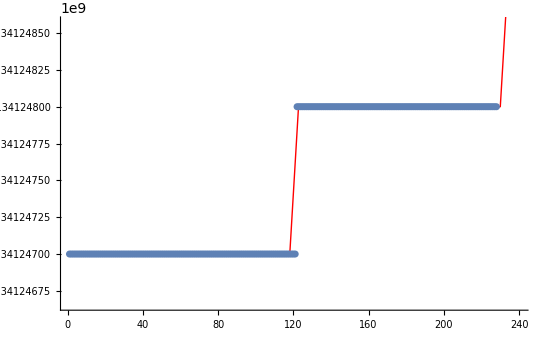

```mathematica
tablex//ListPlot;
Fit[tablex,{1,y,1/y,1/y^2},y];
Show[Plot[%,{y,1,max/step 4},PlotStyle->{Red,Thick}],%%]
```

## Export

```mathematica
Export[NotebookDirectory[]<>"oldplot.pdf",oldplot]
```

/Users/Tom/Mathematica/msstp/2014/Day4/oldplot.pdf

```mathematica
Export[NotebookDirectory[]<>"oldplot2.pdf",oldplot,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

/Users/Tom/Mathematica/msstp/2014/Day4/oldplot2.pdf

```mathematica
Export[NotebookDirectory[]<>"plot3d.pdf",plot3d,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

/Users/Tom/Mathematica/msstp/2014/Day4/plot3d.pdf

```mathematica
plot3d
```

-Graphics3D-

## ϵ Expansion

For d=4-ϵ

```mathematica
Δσ4d=(4-ϵ)/2-1+0.0185 ϵ^2+0.0187 ϵ^3-0.0083 ϵ^4+0.0257 ϵ^5;
Δϵ4d=4-ϵ-(2-1/3 ϵ-0.117 ϵ^2+0.124 ϵ^3-0.307 ϵ^4+0.951 ϵ^5);
```

```mathematica
Δσ2d=1/8;
Δϵ2d=1;
```

```mathematica
Δσ6d=2-0.5501 (2+ϵ);
Δϵ6d=2-0.5611 (2+ϵ);
```

```mathematica
Δσ4d
```

-1+(4-ϵ)/2+0.0185 ϵ^2+0.0187 ϵ^3-0.0083 ϵ^4+0.0257 ϵ^5

```mathematica
Manipulate[Block[{fn},
fn={Δσ4d/.ϵ^(n_.):>0/;n>p,Δϵ4d/.ϵ^(n_.):>0/;n>p};
Plot[fn,{ϵ,0,2}]],{p,1,5,1},ControlType->SetterBar];
```

```mathematica
pade=(Δ0+𝕒 ϵ+𝕓 ϵ^2+𝕔 ϵ^3+𝕕 ϵ^4+𝔻 ϵ^5)/(1+𝔸 ϵ+𝔹 ϵ^2+ℂ ϵ^3);
```

```mathematica
4-ϵ
```

4-ϵ

```mathematica
(pade/.ϵ->2)==Δσ2d∧Series[pade,{ϵ,0,5}]==Δσ4d∧Series[pade,{ϵ,-2,1}]==Δσ6d//LogicalExpand//Solve//First;
improvedσ=pade/.%/.ϵ->1
```

0.528885

```mathematica
(pade/.ϵ->2)==Δϵ2d∧Series[pade,{ϵ,0,5}]==Δϵ4d∧Series[pade,{ϵ,-2,1}]==Δϵ6d//LogicalExpand//Solve//First;
improvedϵ=(padeϵ=pade/.%)/.ϵ->1
```

1.41395

## The image and some markers

```mathematica
image=-Graphics-;
```

```mathematica
DynamicModule[{pt={{300,300},{300,300}}},{LocatorPane[Dynamic[pt],image],Dynamic[PT=pt]}]
```

```mathematica
PT
```

PT

```mathematica
prediction={PT⟦1,1⟧+(PT⟦2,1⟧-PT⟦1,1⟧)/(.1)(improvedσ-.5),PT⟦2,2⟧+(PT⟦1,2⟧-PT⟦2,2⟧)/(.7)(improvedϵ-1)};
point=Graphics[{Red,PointSize[0.008],Point[prediction]}];
```

## The result

```mathematica
Show[image,point]
```

-Graphics-